```mathematica
{ol500c24h,ol500c24hkeep,ol500c24hkill,ol500c24hmem,oltyp}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\ol500c24htest.mx"];
```

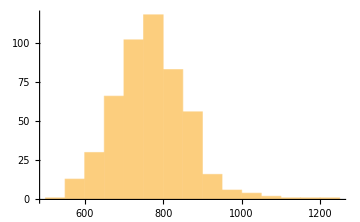

```mathematica
Histogram[ol500c24h[[1]][[4]]/ol500c24h[[1]][[6]],AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
{hmu400gen,hmu800gen,hmu1400gen,hmu400keep,hmu800keep,hmu1400keep,hmu400kill,hmu800kill,hmu1400kill,hmu400mem,hmu800mem,hmu1400mem,hmu400typ,hmu800typ,hmu1400typ}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hmu500c24htest.mx"];
```

```mathematica
{hmutyp500,hmutyp600,hmutyp700,hmutyp900,hmutyp1000,hmutyp1100,hmutyp1200,hmutyp1300}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hmutyp.mx"];
```

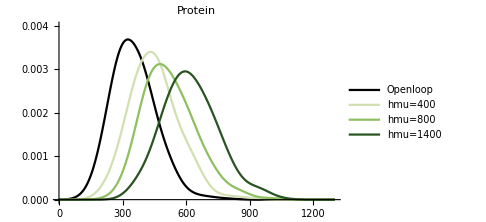

```mathematica
SmoothHistogram[{ol500c24h[[1]][[1]]/ol500c24h[[1]][[6]],hmu400gen[[1]][[1]]/hmu400gen[[1]][[6]],hmu800gen[[1]][[1]]/hmu800gen[[1]][[6]],hmu1400gen[[1]][[1]]/hmu1400gen[[1]][[6]]},50,PlotRange->{{0,1300},{0,0.004}},PlotLegends->{"Openloop","hmu=400","hmu=800","hmu=1400"},PlotLabel->Style["Protein",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#d1dfb1"],Thick],Directive[RGBColor["#8ebf60"],Thick],Directive[RGBColor["#295421"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

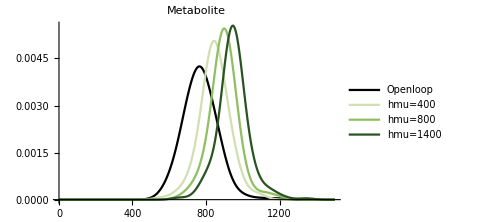

```mathematica
SmoothHistogram[{ol500c24h[[1]][[4]]/ol500c24h[[1]][[6]],hmu400gen[[1]][[4]]/hmu400gen[[1]][[6]],hmu800gen[[1]][[4]]/hmu800gen[[1]][[6]],hmu1400gen[[1]][[4]]/hmu1400gen[[1]][[6]]},40,PlotRange->{{0,1500},Automatic},PlotLegends->{"Openloop","hmu=400","hmu=800","hmu=1400"},PlotLabel->Style["Metabolite",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#d1dfb1"],Thick],Directive[RGBColor["#8ebf60"],Thick],Directive[RGBColor["#295421"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

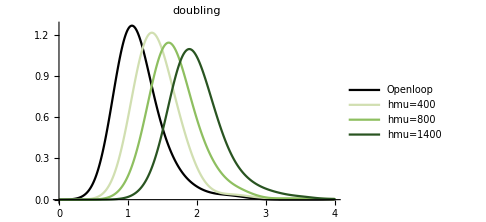

```mathematica
SmoothHistogram[{Log[2]/ol500c24h[[1]][[5]],Log[2]/hmu400gen[[1]][[5]],Log[2]/hmu800gen[[1]][[5]],Log[2]/hmu1400gen[[1]][[5]]},0.2,PlotRange->{{0,4},Automatic},PlotLegends->{"Openloop","hmu=400","hmu=800","hmu=1400"},PlotLabel->Style["doubling",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#d1dfb1"],Thick],Directive[RGBColor["#8ebf60"],Thick],Directive[RGBColor["#295421"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

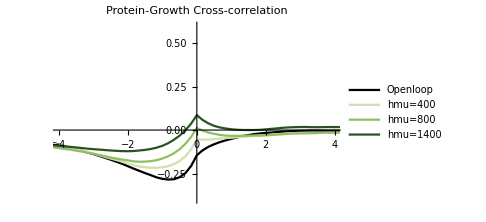

```mathematica
ListLinePlot[{ol500c24hmem[[4]],hmu400mem[[4]],hmu800mem[[4]],hmu1400mem[[4]]},PlotRange->{{-4,4},{-0.4,0.6}},PlotLegends->{"Openloop","hmu=400","hmu=800","hmu=1400"},PlotLabel->Style["Protein-Growth Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#d1dfb1"],Thick],Directive[RGBColor["#8ebf60"],Thick],Directive[RGBColor["#295421"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

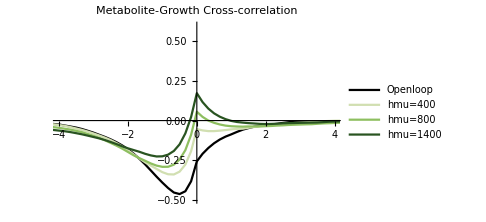

```mathematica
ListLinePlot[{ol500c24hmem[[5]],hmu400mem[[5]],hmu800mem[[5]],hmu1400mem[[5]]},PlotRange->{{-4,4},{-0.5,0.6}},PlotLegends->{"Openloop","hmu=400","hmu=800","hmu=1400"},PlotLabel->Style["Metabolite-Growth Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#d1dfb1"],Thick],Directive[RGBColor["#8ebf60"],Thick],Directive[RGBColor["#295421"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

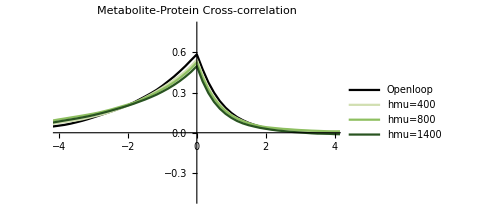

```mathematica
ListLinePlot[{ol500c24hmem[[6]],hmu400mem[[6]],hmu800mem[[6]],hmu1400mem[[6]]},PlotRange->{{-4,4},{-0.5,0.8}},PlotLegends->{"Openloop","hmu=400","hmu=800","hmu=1400"},PlotLabel->Style["Metabolite-Protein Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#d1dfb1"],Thick],Directive[RGBColor["#8ebf60"],Thick],Directive[RGBColor["#295421"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

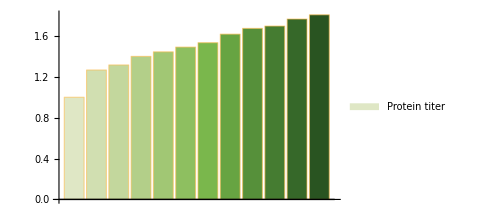

```mathematica
BarChart[{oltyp[[2]]/oltyp[[2]],hmu400typ[[2]]/oltyp[[2]],hmutyp500[[2]]/oltyp[[2]],hmutyp600[[2]]/oltyp[[2]],hmutyp700[[2]]/oltyp[[2]],hmu800typ[[2]]/oltyp[[2]],hmutyp900[[2]]/oltyp[[2]],hmutyp1000[[2]]/oltyp[[2]],hmutyp1100[[2]]/oltyp[[2]],hmutyp1200[[2]]/oltyp[[2]],hmutyp1300[[2]]/oltyp[[2]],hmu1400typ[[2]]/oltyp[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#dfe7c5"],
RGBColor["#d1dfb1"],
RGBColor["#c3d79d"],
RGBColor["#b3cf89"],
RGBColor["#a1c774"],
RGBColor["#8ebf60"],
RGBColor["#7ab74c"],
RGBColor["#67a442"],
RGBColor["#56903a"],
RGBColor["#457c31"],
RGBColor["#366829"],
RGBColor["#295421"]
},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

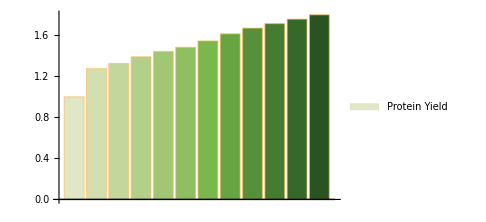

```mathematica
BarChart[{oltyp[[5]]/oltyp[[5]],hmu400typ[[5]]/oltyp[[5]],hmutyp500[[5]]/oltyp[[5]],hmutyp600[[5]]/oltyp[[5]],hmutyp700[[5]]/oltyp[[5]],hmu800typ[[5]]/oltyp[[5]],hmutyp900[[5]]/oltyp[[5]],hmutyp1000[[5]]/oltyp[[5]],hmutyp1100[[5]]/oltyp[[5]],hmutyp1200[[5]]/oltyp[[5]],hmutyp1300[[5]]/oltyp[[5]],hmu1400typ[[5]]/oltyp[[5]]},ChartLegends->{"Protein Yield"},ChartStyle->{RGBColor["#dfe7c5"],
RGBColor["#d1dfb1"],
RGBColor["#c3d79d"],
RGBColor["#b3cf89"],
RGBColor["#a1c774"],
RGBColor["#8ebf60"],
RGBColor["#7ab74c"],
RGBColor["#67a442"],
RGBColor["#56903a"],
RGBColor["#457c31"],
RGBColor["#366829"],
RGBColor["#295421"]
},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

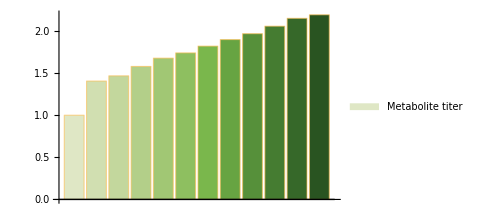

```mathematica
BarChart[{oltyp[[4]]/oltyp[[4]],hmu400typ[[4]]/oltyp[[4]],hmutyp500[[4]]/oltyp[[4]],hmutyp600[[4]]/oltyp[[4]],hmutyp700[[4]]/oltyp[[4]],hmu800typ[[4]]/oltyp[[4]],hmutyp900[[4]]/oltyp[[4]],hmutyp1000[[4]]/oltyp[[4]],hmutyp1100[[4]]/oltyp[[4]],hmutyp1200[[4]]/oltyp[[4]],hmutyp1300[[4]]/oltyp[[4]],hmu1400typ[[4]]/oltyp[[4]]},ChartLegends->{"Metabolite titer"},ChartStyle->{RGBColor["#dfe7c5"],
RGBColor["#d1dfb1"],
RGBColor["#c3d79d"],
RGBColor["#b3cf89"],
RGBColor["#a1c774"],
RGBColor["#8ebf60"],
RGBColor["#7ab74c"],
RGBColor["#67a442"],
RGBColor["#56903a"],
RGBColor["#457c31"],
RGBColor["#366829"],
RGBColor["#295421"]
},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

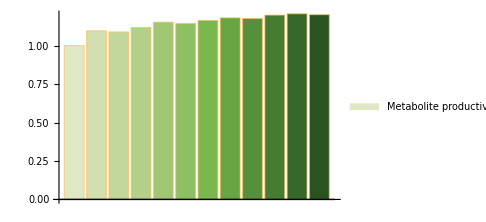

```mathematica
BarChart[{oltyp[[9]]/oltyp[[9]],hmu400typ[[9]]/oltyp[[9]],hmutyp500[[9]]/oltyp[[9]],hmutyp600[[9]]/oltyp[[9]],hmutyp700[[9]]/oltyp[[9]],hmu800typ[[9]]/oltyp[[9]],hmutyp900[[9]]/oltyp[[9]],hmutyp1000[[9]]/oltyp[[9]],hmutyp1100[[9]]/oltyp[[9]],hmutyp1200[[9]]/oltyp[[9]],hmutyp1300[[9]]/oltyp[[9]],hmu1400typ[[9]]/oltyp[[9]]},PlotRange->{0,1.2},ChartLegends->{"Metabolite productivity"},ChartStyle->{RGBColor["#dfe7c5"],
RGBColor["#d1dfb1"],
RGBColor["#c3d79d"],
RGBColor["#b3cf89"],
RGBColor["#a1c774"],
RGBColor["#8ebf60"],
RGBColor["#7ab74c"],
RGBColor["#67a442"],
RGBColor["#56903a"],
RGBColor["#457c31"],
RGBColor["#366829"],
RGBColor["#295421"]
},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
{hmugen1,hmugen10,hmugen50,hmugen90,hmugen99,hmukeep1,hmukeep10,hmukeep50,hmukeep90,hmukeep99,hmumem1,hmumem10,hmumem50,hmumem90,hmumem99,hmukill1,hmukill10,hmukill50,hmukill90,hmukill99,hmutyp1,hmutyp10,hmutyp50,hmutyp90,hmutyp99}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hmu500c24hpercent.mx"];
```

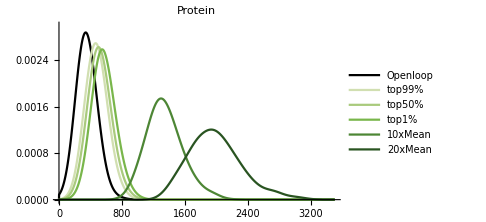

```mathematica
SmoothHistogram[{ol500c24h[[1]][[1]]/ol500c24h[[1]][[6]],hmugen1[[1]][[1]]/hmugen1[[1]][[6]],hmugen50[[1]][[1]]/hmugen50[[1]][[6]],hmugen99[[1]][[1]]/hmugen99[[1]][[6]],hmugen7000[[1]][[1]]/hmugen7000[[1]][[6]],hmugen14000[[1]][[1]]/hmugen14000[[1]][[6]]},100,PlotRange->{{0,3500},{0,0.003}},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Protein",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#d1dfb1"],Thick],Directive[RGBColor["#a9ca7d"],Thick],Directive[RGBColor["#79b64b"],Thick],Directive[RGBColor["#4d8635"],Thick],Directive[RGBColor["#295421"],Thick]},AxesStyle->Directive[Black, 14],ImageSize->Medium]
```

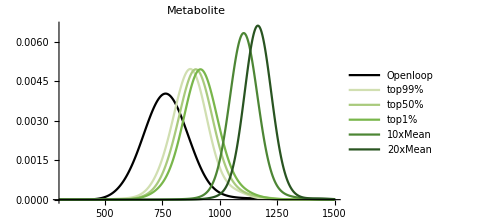

```mathematica
SmoothHistogram[{ol500c24h[[1]][[4]]/ol500c24h[[1]][[6]],hmugen1[[1]][[4]]/hmugen1[[1]][[6]],hmugen50[[1]][[4]]/hmugen50[[1]][[6]],hmugen99[[1]][[4]]/hmugen99[[1]][[6]],hmugen7000[[1]][[4]]/hmugen7000[[1]][[6]],hmugen14000[[1]][[4]]/hmugen14000[[1]][[6]]},50,PlotRange->{{300,1500},Automatic},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Metabolite",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#d1dfb1"],Thick],Directive[RGBColor["#a9ca7d"],Thick],Directive[RGBColor["#79b64b"],Thick],Directive[RGBColor["#4d8635"],Thick],Directive[RGBColor["#295421"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

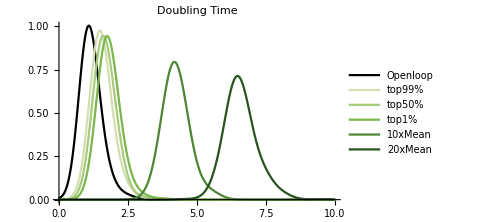

```mathematica
SmoothHistogram[{Log[2]/ol500c24h[[1]][[5]],Log[2]/hmugen1[[1]][[5]],Log[2]/hmugen50[[1]][[5]],Log[2]/hmugen99[[1]][[5]],Log[2]/hmugen7000[[1]][[5]],Log[2]/hmugen14000[[1]][[5]]},0.3,PlotRange->{{0,10},Automatic},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Doubling Time",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#d1dfb1"],Thick],Directive[RGBColor["#a9ca7d"],Thick],Directive[RGBColor["#79b64b"],Thick],Directive[RGBColor["#4d8635"],Thick],Directive[RGBColor["#295421"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
hmumem7000=metabproteinmemfast[hmukeep7000];
```

```mathematica
hmumem14000=metabproteinmemfast[hmukeep14000];
```

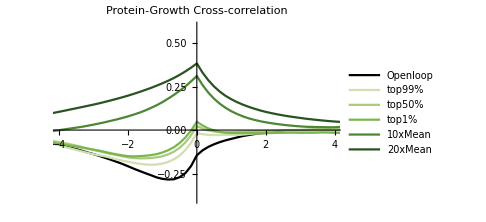

```mathematica
ListLinePlot[{ol500c24hmem[[4]],hmumem1[[4]],hmumem50[[4]],hmumem99[[4]],hmumem7000[[4]],hmumem14000[[4]]},PlotRange->{{-4,4},{-0.4,0.6}},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Protein-Growth Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#d1dfb1"],Thick],Directive[RGBColor["#a9ca7d"],Thick],Directive[RGBColor["#79b64b"],Thick],Directive[RGBColor["#4d8635"],Thick],Directive[RGBColor["#295421"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

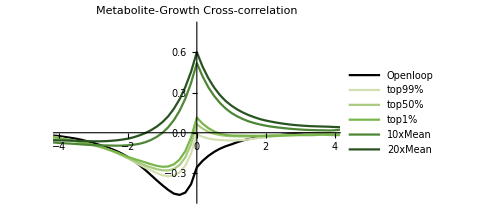

```mathematica
ListLinePlot[{ol500c24hmem[[5]],hmumem1[[5]],hmumem50[[5]],hmumem99[[5]],hmumem7000[[5]],hmumem14000[[5]]},PlotRange->{{-4,4},{-0.5,0.8}},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Metabolite-Growth Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#d1dfb1"],Thick],Directive[RGBColor["#a9ca7d"],Thick],Directive[RGBColor["#79b64b"],Thick],Directive[RGBColor["#4d8635"],Thick],Directive[RGBColor["#295421"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

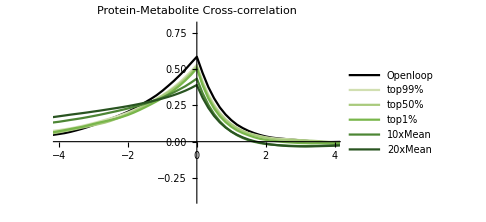

```mathematica
ListLinePlot[{ol500c24hmem[[6]],hmumem1[[6]],hmumem50[[6]],hmumem99[[6]],hmumem7000[[6]],hmumem14000[[6]]},PlotRange->{{-4,4},{-0.4,0.8}},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Protein-Metabolite Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#d1dfb1"],Thick],Directive[RGBColor["#a9ca7d"],Thick],Directive[RGBColor["#79b64b"],Thick],Directive[RGBColor["#4d8635"],Thick],Directive[RGBColor["#295421"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

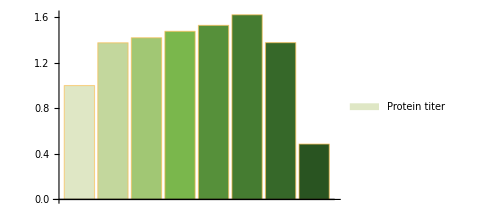

```mathematica
BarChart[{oltyp[[2]]/oltyp[[2]],hmutyp1[[2]]/oltyp[[2]],hmutyp10[[2]]/oltyp[[2]],hmutyp50[[2]]/oltyp[[2]],hmutyp90[[2]]/oltyp[[2]],hmutyp99[[2]]/oltyp[[2]],hmutyp7000[[2]]/oltyp[[2]],hmutyp14000[[2]]/oltyp[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#dfe7c5"],

RGBColor["#c3d79d"],

RGBColor["#a1c774"],

RGBColor["#7ab74c"],

RGBColor["#56903a"],
RGBColor["#457c31"],
RGBColor["#366829"],
RGBColor["#295421"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

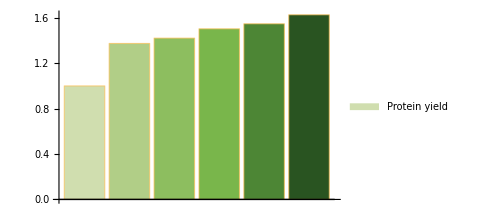

```mathematica
BarChart[{oltyp[[5]]/oltyp[[5]],hmutyp1[[5]]/oltyp[[5]],hmutyp10[[5]]/oltyp[[5]],hmutyp50[[5]]/oltyp[[5]],hmutyp90[[5]]/oltyp[[5]],hmutyp99[[5]]/oltyp[[5]]},ChartLegends->{"Protein yield"},ChartStyle->{RGBColor["#d0deaf"],
RGBColor["#b1ce87"],
RGBColor["#8dbe5f"],
RGBColor["#79b64b"],
RGBColor["#4d8635"],
RGBColor["#295421"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

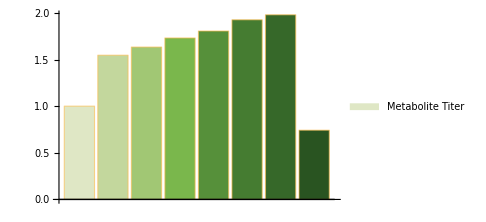

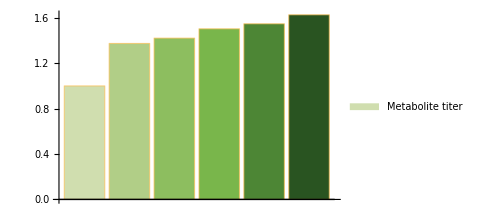

```mathematica
BarChart[{oltyp[[4]]/oltyp[[4]],hmutyp1[[4]]/oltyp[[4]],hmutyp10[[4]]/oltyp[[4]],hmutyp50[[4]]/oltyp[[4]],hmutyp90[[4]]/oltyp[[4]],hmutyp99[[4]]/oltyp[[4]],hmutyp7000[[4]]/oltyp[[4]],hmutyp14000[[4]]/oltyp[[4]]},ChartLegends->{"Metabolite Titer"},ChartStyle->{RGBColor["#dfe7c5"],

RGBColor["#c3d79d"],

RGBColor["#a1c774"],

RGBColor["#7ab74c"],

RGBColor["#56903a"],
RGBColor["#457c31"],
RGBColor["#366829"],
RGBColor["#295421"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
hmutyp7000=titeryieldproductivity[hmukill7000]
```

```mathematica
hmutyp14000=titeryieldproductivity[hmukill14000];
```

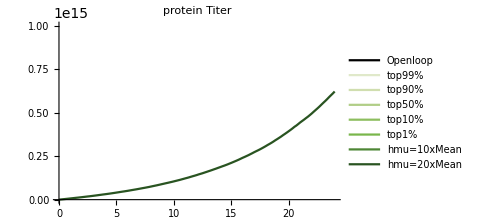

```mathematica
ListLinePlot[{oltyp[[1]],hmutyp1[[1]],hmutyp10[[1]],hmutyp50[[1]],hmutyp90[[1]],hmutyp99[[1]],hmutyp7000[[1]],hmutyp14000[[1]]},PlotLabel->"protein Titer",PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%","hmu=10xMean","hmu=20xMean"},PlotStyle->{Black,Lighter[RGBColor["#d0deaf"]],RGBColor["#d0deaf"],
RGBColor["#b1ce87"],
RGBColor["#8dbe5f"],
RGBColor["#79b64b"],
RGBColor["#4d8635"],
RGBColor["#295421"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
ListLinePlot[{oltyp[[3]],hmutyp1[[3]],hmutyp10[[3]],hmutyp50[[3]],hmutyp90[[3]],hmutyp99[[3]],hmutyp7000[[3]],hmutyp14000[[3]]},PlotLabel->"metabolite Titer",PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%","10xMean","20xMean"},PlotStyle->{Black,Lighter[RGBColor["#d0deaf"]],RGBColor["#d0deaf"],
RGBColor["#b1ce87"],
RGBColor["#8dbe5f"],
RGBColor["#79b64b"],
RGBColor["#4d8635"],
RGBColor["#295421"]},AxesStyle->Directive[Black, 16],ImageSize->Medium,PlotRange->{{0,24},{0,9*10^15}}]
```

-Graphics-